#### Relaciones de recurrencia

c(t) es el ahorro en el mes t, la constnte ies el ingreso neto que se puede ahrorar, y es contante

```mathematica
i=200;
c[0]=200;
c[t_]:=c[t-1]+ i;
```

```mathematica
c[10]
```

2200

Ahorro en un año crece...

```mathematica
datos=Table[c[t],{t,0,12}];
```

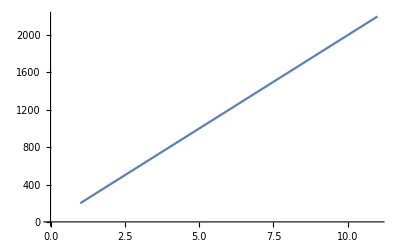

```mathematica
ListLinePlot[datos]
```

el ingreso es constante en el año

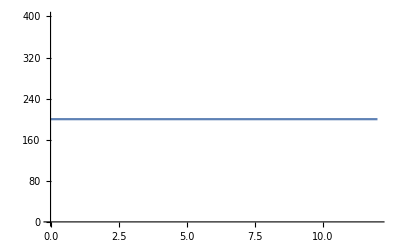

```mathematica
Plot[i,{x,0,12}]
```